# Levels

## Avicii

Arranged by Traci Johnson
Created May 23, 2012

Oh, sometimes I get a good feeling... yeah.

## Notes

Sometimes I get the feeling where I want to sit in front of my computer for hours on end and write a song in Mathematica. But there's nothing like the good feeling I get when I finish it. Hopefully you'll get a good feeling listening to the newest addition to my collection of Mathematica songs.

No need to evaluate anything in this notebook. Simply press the play button on the bottom left of the sound box graphic thing below. But if you wish, simply double click on the side bracket next to the sound output box to expand the code I used to write this song and feel free to write your own remix.

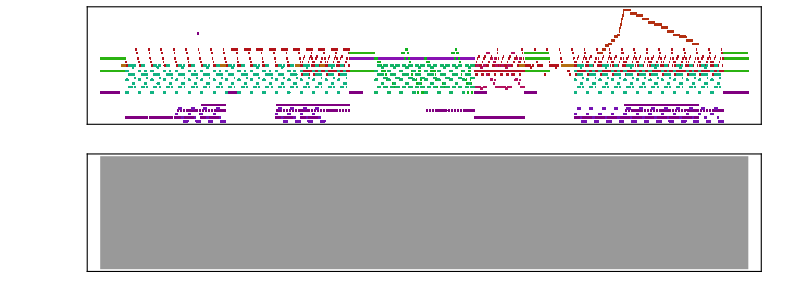

```mathematica
introChords=Sound[{Table[{SoundNote[None, 0.5x],SoundNote[{"C#4","G#4"},0.5x,"SynthStrings"]},{n,1,17}]}];

introCrash=Sound[{Table[SoundNote["CrashCymbal",x,SoundVolume->(12-n)/12],{n,1,12}],SoundNote[None,x],SoundNote["E4",3x,"ReverseCymbal"]}];

jingle=Sound[{
SoundNote["F#4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote[None,0.5x],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["D#4",0.5x,"BrightPiano"],
SoundNote["D#4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote[None,0.5x],
SoundNote["C#5",0.5x,"BrightPiano"],
SoundNote["B4",0.5x,"BrightPiano"],
SoundNote["G#4",0.5x,"BrightPiano"],
SoundNote["F#4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote[None,0.5x],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["E4",0.5x,"BrightPiano"],
SoundNote["C#4",0.5x,"BrightPiano"],
SoundNote["C#4",0.5x,"BrightPiano"],
SoundNote["B3",0.5x,"BrightPiano"],
SoundNote["B3",0.5x,"BrightPiano"],
SoundNote[None,0.5x],
SoundNote["C#5",0.5x,"BrightPiano"],
SoundNote["B4",0.5x,"BrightPiano"],
SoundNote["G#4",0.5x,"BrightPiano"]
}];

chords=Sound[{
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness"],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness"],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness"],
SoundNote[None,0.5x],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"B3","F#3","D#4"},0.5x,"Brightness"],
SoundNote[{"B3","F#3","D#4"},0.5x,"Brightness"],
SoundNote[{"B3","F#3","E4"},0.5x,"Brightness"],
SoundNote[{"A3","E3","E4"},0.5x,"Brightness"],
SoundNote[None,2x],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness"],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness"],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness"],
SoundNote[None,0.5x],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness"],
SoundNote[{"B3","F#3","C#4"},0.5x,"Brightness"],
SoundNote[{"B3","F#3","C#4"},0.5x,"Brightness"],
SoundNote[{"B3","F#3","B3"},0.5x,"Brightness"],
SoundNote[{"A3","E3","B3"},0.5x,"Brightness"],
SoundNote[None,2x]
}];

bassDrumKick=Sound[{
Table[SoundNote["BassDrum",x],{n,1,6}],SoundNote[None,x],
Table[SoundNote["BassDrum",x],{n,1,7}],SoundNote[None,x],SoundNote["BassDrum",x]}];

boom=Sound[{
Table[SoundNote["BassDrum",x],{n,1,16}]}];

halfboom=Sound[{
Table[SoundNote["BassDrum",x],{n,1,12}],
SoundNote[None,2x],
SoundNote["Shaker",1/6x,SoundVolume->0.5],
SoundNote["Shaker",1/6x,SoundVolume->0.5],
SoundNote["Shaker",1/6x,SoundVolume->0.5],
SoundNote[None,0.5x],
SoundNote["SideStick",x]
}];

chick=Sound[{
Table[{SoundNote[None,x],SoundNote["Clap",x]},{n,1,8}]}];

bassLine=Sound[{
SoundNote["C#2",0.5x,"BassAndLead"],
SoundNote["C#2",0.5x,"BassAndLead"],
SoundNote["C#2",0.5x,"BassAndLead"],
SoundNote[None,0.5x],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["B1",0.5x,"BassAndLead"],
SoundNote["B1",0.5x,"BassAndLead"],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote[None,0.5x],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote[None,0.5x],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote["C#2",0.5x,"BassAndLead"],
SoundNote["C#2",0.5x,"BassAndLead"],
SoundNote["C#2",0.5x,"BassAndLead"],
SoundNote[None,0.5x],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["E2",0.5x,"BassAndLead"],
SoundNote["B1",0.5x,"BassAndLead"],
SoundNote["B1",0.5x,"BassAndLead"],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote[None,0.5x],
SoundNote["A1",0.5x,"BassAndLead"],
SoundNote[None,0.5x],
SoundNote["A1",0.5x,"BassAndLead"]
}];

hiHat=Sound[{
Table[{SoundNote[None,0.5x],SoundNote["HiHatClosed",0.25x],SoundNote["HiHatClosed",0.25x]},{n,1,16}]}];

halfboom2=Sound[{
Table[SoundNote["BassDrum",x],{n,1,12}],
SoundNote[None,x],
SoundNote["E4",3x,"ReverseCymbal"]
}];

cymbals=Sound[Table[SoundNote["CrashCymbal",x,SoundVolume->(8-n)/8],{n,1,8}]];

whine=Sound[{
SoundNote["E4",4x,"Flute"],
SoundNote["C#5",4x,"Flute"],
SoundNote["E4",4x,"Flute"],
SoundNote["C#5",4x,"Flute"]
}];

jingleCrescendo[n_,m_]=Sound[{
SoundNote["F#4",0.5x,"BrightPiano",SoundVolume->(n+1)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+2)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+3)/m],
SoundNote[None,0.5x],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+5)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+6)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+7)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+8)/m],
SoundNote["D#4",0.5x,"BrightPiano",SoundVolume->(n+9)/m],
SoundNote["D#4",0.5x,"BrightPiano",SoundVolume->(n+10)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+11)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+12)/m],
SoundNote[None,0.5x],
SoundNote["C#5",0.5x,"BrightPiano",SoundVolume->(n+14)/m],
SoundNote["B4",0.5x,"BrightPiano",SoundVolume->(n+15)/m],
SoundNote["G#4",0.5x,"BrightPiano",SoundVolume->(n+16)/m],
SoundNote["F#4",0.5x,"BrightPiano",SoundVolume->(n+17)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+18)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+19)/m],
SoundNote[None,0.5x],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+21)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+22)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+23)/m],
SoundNote["E4",0.5x,"BrightPiano",SoundVolume->(n+24)/m],
SoundNote["C#4",0.5x,"BrightPiano",SoundVolume->(n+25)/m],
SoundNote["C#4",0.5x,"BrightPiano",SoundVolume->(n+26)/m],
SoundNote["B3",0.5x,"BrightPiano",SoundVolume->(n+27)/m],
SoundNote["B3",0.5x,"BrightPiano",SoundVolume->(n+28)/m],
SoundNote[None,0.5x],
SoundNote["C#5",0.5x,"BrightPiano",SoundVolume->(n+30)/m],
SoundNote["B4",0.5x,"BrightPiano",SoundVolume->(n+31)/m],
SoundNote["G#4",0.5x,"BrightPiano",SoundVolume->(n+32)/m]
}];

chordsCrescendo[n_,m_]=Sound[{
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness",SoundVolume->(n+1)/m],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness",SoundVolume->(n+2)/m],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness",SoundVolume->(n+3)/m],
SoundNote[None,0.5x],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+5)/m],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+6)/m],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+7)/m],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+8)/m],
SoundNote[{"B3","F#3","D#4"},0.5x,"Brightness",SoundVolume->(n+9)/m],
SoundNote[{"B3","F#3","D#4"},0.5x,"Brightness",SoundVolume->(n+10)/m],
SoundNote[{"B3","F#3","E4"},0.5x,"Brightness",SoundVolume->(n+11)/m],
SoundNote[{"A3","E3","E4"},0.5x,"Brightness",SoundVolume->(n+12)/m],
SoundNote[None,2x],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness",SoundVolume->(n+14)/m],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness",SoundVolume->(n+15)/m],
SoundNote[{"C#3","G#3","C#4"},0.5x,"Brightness",SoundVolume->(n+16)/m],
SoundNote[None,0.5x],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+18)/m],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+19)/m],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+20)/m],
SoundNote[{"E3","B3","E4"},0.5x,"Brightness",SoundVolume->(n+21)/m],
SoundNote[{"B3","F#3","C#4"},0.5x,"Brightness",SoundVolume->(n+22)/m],
SoundNote[{"B3","F#3","C#4"},0.5x,"Brightness",SoundVolume->(n+23)/m],
SoundNote[{"B3","F#3","B3"},0.5x,"Brightness",SoundVolume->(n+24)/m],
SoundNote[{"A3","E3","B3"},0.5x,"Brightness",SoundVolume->(n+25)/m],
SoundNote[None,2x]
}];

coolRiff=Sound[{
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["F#4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["G#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["A4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["F#4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["G#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["A4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["F#4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["G#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["A4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["F#4",0.25x,"Polysynth"],
SoundNote["B3",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],

SoundNote["G#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["C#5",0.25x,"Polysynth"],
SoundNote["B4",0.25x,"Polysynth"],

SoundNote["C#4",0.25x,"Polysynth"],
SoundNote["E4",0.25x,"Polysynth"],
SoundNote["G#4",0.25x,"Polysynth"],
SoundNote["C#4",0.25x,"Polysynth"]
}];

chorusChordsDecrescendo=Sound[{Table[{SoundNote[{"B4"},0.5x,"SynthStrings",SoundVolume->(16-n)/24],SoundNote[{"C#4","G#4"},0.5x,"SynthStrings",SoundVolume->(16-n)/16]},{n,1,16}]}];

vocals=Sound[{
SoundNote["G#4",1.5x,"Voice"],
SoundNote["F#4",2x,"Voice"],
SoundNote["E4",0.5x,"Voice"],
SoundNote["C#4",2.5x,"Voice"],
SoundNote["C#4",0.5x,"Voice"],
SoundNote["B3",0.25x,"Voice"],
SoundNote["G#3",0.25x,"Voice"],
SoundNote["E3",0.5x,"Voice"],
SoundNote["C#4",0.5x,"Voice"],
SoundNote["C#4",0.5x,"Voice"],
SoundNote[None,2.5x],
SoundNote["F#3",0.5x,"Voice"],
SoundNote["E3",0.5x,"Voice"],
SoundNote[None,4.5x],

SoundNote["B4",0.5x,"Voice"],
SoundNote["B4",0.5x,"Voice"],
SoundNote["B4",0.5x,"Voice"],
SoundNote["B4",0.5x,"Voice"],
SoundNote["G#4",0.5x,"Voice"],
SoundNote["G#4",0.5x,"Voice"],

SoundNote["C#5",0.5x,"Voice"],
SoundNote["C#5",0.25x,"Voice"],
SoundNote["B4",0.5x,"Voice"],
SoundNote["B4",0.25x,"Voice"],
SoundNote["G#4",0.5x,"Voice"],
SoundNote["G#4",0.25x,"Voice"],
SoundNote["F#4",0.5x,"Voice"],
SoundNote["F#4",0.25x,"Voice"],

SoundNote["E4",0.5x,"Voice"],
SoundNote["C#4",0.25x,"Voice"],
SoundNote["B3",0.25x,"Voice"],
SoundNote["C#4",x,"Voice"],

SoundNote["C#4",0.5x,"Voice"],
SoundNote["G#3",0.5x,"Voice"],
SoundNote["E3",0.5x,"Voice"],

SoundNote["G#3",0.5x,"Voice"],
SoundNote["F#3",0.25x,"Voice"],
SoundNote["E3",0.25x,"Voice"],
SoundNote["C#3",0.5x,"Voice"],

SoundNote["C#4",0.5x,"Voice"],
SoundNote["C#4",x,"Voice"],
SoundNote["G#3",0.25x,"Voice"],
SoundNote["F#3",0.25x,"Voice"],
SoundNote["C#3",x,"Voice"]
}];

background[n_,m_]=Sound[{
SoundNote[{"C#3","G#3","C#4"},2x,"Ocarina",SoundVolume->(n+1)/m],
SoundNote[{"E3","B3","E4"},2x,"Ocarina",SoundVolume->(n+2)/m],
SoundNote[{"B3","F#3","D#4"},1.5x,"Ocarina",SoundVolume->(n+3)/m],
SoundNote[{"A3","E3","E4"},2.5x,"Ocarina",SoundVolume->(n+4)/m],

SoundNote[{"C#3","G#3","C#4"},2x,"Ocarina",SoundVolume->(n+5)/m],
SoundNote[{"E3","B3","E4"},2x,"Ocarina",SoundVolume->(n+6)/m],
SoundNote[{"B3","F#3","D#4"},1.5x,"Ocarina",SoundVolume->(n+7)/m],
SoundNote[{"A3","E3","E4"},2.5x,"Ocarina",SoundVolume->(n+8)/m],

SoundNote[{"C#3","G#3","C#4"},2x,"Ocarina",SoundVolume->(n+9)/m],
SoundNote[{"E3","B3","E4"},2x,"Ocarina",SoundVolume->(n+10)/m],
SoundNote[{"B3","F#3","D#4"},1.5x,"Ocarina",SoundVolume->(n+11)/m],
SoundNote[{"A3","E3","E4"},2.5x,"Ocarina",SoundVolume->(n+12)/m],

SoundNote[{"C#3","G#3","C#4"},2x,"Ocarina",SoundVolume->(n+13)/m],
SoundNote[{"E3","B3","E4"},2x,"Ocarina",SoundVolume->(n+14)/m],
SoundNote[{"B3","F#3","D#4"},1.5x,"Ocarina",SoundVolume->(n+15)/m],
SoundNote[{"A3","E3","E4"},2.5x,"Ocarina",SoundVolume->(n+16)/m]
}];

chorusEndStrings=Sound[{
SoundNote[{"E3","E4"},2x,"Strings"],
SoundNote[{"E3","E4"},2x,"Strings"],
SoundNote[{"D#3","D#4"},1.5x,"Strings"],
SoundNote[{"E3","E4"},2.5x,"Strings"],

SoundNote[{"B3","B4"},2x,"Strings"],
SoundNote[{"G#3","G#4"},2x,"Strings"],
SoundNote[{"F#3","F#4"},1x,"Strings"],
SoundNote[{"G#3","G#4"},0.5x,"Strings"],
SoundNote[{"E3","E4"},2.5x,"Strings"]
}];

sweepup=Sound[{
Table[SoundNote["B4",0.25x,"ElectricPiano2"],{n,1,8}],
Table[SoundNote["C#5",0.25x,"ElectricPiano2"],{n,1,8}],
Table[SoundNote["D#5",0.25x,"ElectricPiano2"],{n,1,8}],
Table[SoundNote["E5",0.25x,"ElectricPiano2"],{n,1,8}],
Table[SoundNote["F#5",0.25x,"ElectricPiano2"],{n,1,8}],
Table[SoundNote["G#5",0.25x,"ElectricPiano2"],{n,1,8}],
Table[SoundNote["A5",0.25x,"ElectricPiano2"],{n,1,4}],
SoundNote["B5",0.25x,"ElectricPiano2"],
SoundNote["C6",0.25x,"ElectricPiano2"],
SoundNote["C#6",0.25x,"ElectricPiano2"],
SoundNote["D6",0.25x,"ElectricPiano2"],
SoundNote["D#6",0.25x,"ElectricPiano2"],
SoundNote["E6",0.25x,"ElectricPiano2"],
SoundNote["F6",0.25x,"ElectricPiano2"],
SoundNote["F#6",0.25x,"ElectricPiano2"],
SoundNote["G6",0.25x,"ElectricPiano2"],
SoundNote["G#6",0.25x,"ElectricPiano2"],
SoundNote["A6",0.25x,"ElectricPiano2"],
SoundNote["A#6",0.25x,"ElectricPiano2"]
}];

sweepdown=Sound[{
Table[SoundNote["B6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["A6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["G#6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["F#6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["E6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["D#6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["C#6",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["B5",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["A5",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["G#5",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["F#5",0.25x,"ElectricPiano2"],{n,1,16}],
Table[SoundNote["E5",0.25x,"ElectricPiano2"],{n,1,16}]
}];

fadeoutChords=Sound[{Table[{SoundNote[{"B4"},0.5x,"SynthStrings",SoundVolume->(32-n)/48],SoundNote[{"C#4","G#4"},0.5x,"SynthStrings",SoundVolume->(32-n)/32]},{n,1,32}]}];

fadeoutCymbals=Sound[Table[SoundNote["CrashCymbal",x,SoundVolume->(16-n)/16],{n,1,16}]];

(*=============================================================================*)
x=0.47;
b=x;
Sound[{

(* intro *)
Sound[introChords,{-1x+b,16x+b},SoundVolume->0.8],Sound[introCrash,{0x+b,16x+b},SoundVolume->0.9],

(* start jingle *)
Sound[jingle,{16x+b,32x+b},SoundVolume->0.8],Sound[chords,{16x+b,30x+b},SoundVolume->0.8],Sound[bassDrumKick,{16x+b,32x+b},SoundVolume->0.9],

Sound[jingle,{32x+b,48x+b},SoundVolume->0.8],Sound[chords,{32x+b,46x+b},SoundVolume->0.8],Sound[bassDrumKick,{32x+b,48x+b},SoundVolume->0.9],

(* boom chick *)
Sound[jingle,{48x+b,64x+b},SoundVolume->0.8],Sound[chords,{48x+b,62x+b},SoundVolume->0.8],
Sound[bassLine,{48x+b,64x+b},SoundVolume->0.8],
Sound[halfboom,{48x+b,64x+b}],Sound[chick,{48x+b,64x+b}],

(* enter hi-hat *)
SoundNote["CrashCymbal",{64x+b,65x+b}],
Sound[jingle,{64x+b,80x+b},SoundVolume->0.8],Sound[chords,{64x+b,78x+b},SoundVolume->0.8],
Sound[bassLine,{64x+b,80x+b},SoundVolume->0.8],
Sound[halfboom2,{64x+b,80x+b}],Sound[chick,{64x+b,80x+b}],
Sound[hiHat,{64x+b,80x+b},SoundVolume->0.7],

(* drum cut-out *)
Sound[cymbals,{80x+b,88x+b},SoundVolume->0.8],
Sound[jingleCrescendo[48,112],{80x+b,96x+b},SoundVolume->0.8],Sound[chordsCrescendo[48,112],{80x+b,94x+b},SoundVolume->0.8],
Sound[whine,{80x+b,96x+b},SoundVolume->0.5],

Sound[jingleCrescendo[80,112],{96x+b,112x+b},SoundVolume->0.8],Sound[chordsCrescendo[80,112],{96x+b,110x+b},SoundVolume->0.8],
Sound[whine,{96x+b,112x+b},SoundVolume->0.5],

(* resume *)
SoundNote["CrashCymbal",{112x+b,113x+b}],
Sound[jingle,{112x+b,128x+b},SoundVolume->0.8],Sound[chords,{112x+b,126x+b},SoundVolume->0.8],
Sound[whine,{112x+b,128x+b},SoundVolume->0.5],
Sound[bassLine,{112x+b,128x+b},SoundVolume->0.8],
Sound[halfboom2,{112x+b,128x+b}],Sound[chick,{112x+b,128x+b}],
Sound[hiHat,{112x+b,128x+b},SoundVolume->0.7],

(* droppin da beats *)
Sound[jingle,{128x+b,144x+b},SoundVolume->0.8],Sound[chords,{128x+b,142x+b},SoundVolume->0.8],
Sound[whine,{128x+b,144x+b},SoundVolume->0.5],
Sound[bassLine,{128x+b,144x+b},SoundVolume->0.8],
Sound[halfboom2,{128x+b,144x+b}],Sound[chick,{128x+b,144x+b}],
Sound[hiHat,{128x+b,144x+b},SoundVolume->0.7],
Sound[coolRiff,{128x+b,144x+b},SoundVolume->0.8],

Sound[jingle,{144x+b,160x+b},SoundVolume->0.8],Sound[chords,{144x+b,158x+b},SoundVolume->0.8],
Sound[whine,{144x+b,160x+b},SoundVolume->0.5],
Sound[chick,{144x+b,160x+b}],
Sound[hiHat,{144x+b,160x+b},SoundVolume->0.7],
Sound[coolRiff,{144x+b,160x+b},SoundVolume->0.8],

(* chorus *)
SoundNote["G#4",{160x+b,176x+b},"VoiceOohs",SoundVolume->0.5],
Sound[cymbals,{160x+b,168x+b},SoundVolume->0.9],
Sound[chorusChordsDecrescendo,{160x+b,176x+b}],

SoundNote["G#4",{176x+b,208x+b},"VoiceOohs",SoundVolume->0.5],
Sound[vocals,{176x+b,207x+b}],
Sound[background[4,36],{176x+b,208x+b},SoundVolume->0.8],

SoundNote["G#4",{208x+b,240x+b},"VoiceOohs",SoundVolume->0.5],
Sound[vocals,{208x+b,239x+b}],
Sound[background[20,36],{208x+b,240x+b},SoundVolume->0.8],
Sound[chick,{208x+b,224x+b},SoundVolume->0.8],Sound[chick,{224x+b,240x+b},SoundVolume->0.8],

(* vocal cut-off *)
Sound[cymbals,{240x+b,248x+b},SoundVolume->0.8],
Sound[boom,{240x+b,256x+b}],
Sound[coolRiff,{240x+b,256x+b},SoundVolume->0.6],
Sound[chorusEndStrings,{240x+b,256x+b},SoundVolume->0.5],

Sound[boom,{256x+b,272x+b}],SoundNote["E4",{269x+b,272x+b},"ReverseCymbal"],
Sound[coolRiff,{256x+b,272x+b},SoundVolume->0.6],
Sound[chorusEndStrings,{256x+b,272x+b},SoundVolume->0.5],

(* jingle reprise *)
Sound[cymbals,{272x+b,280x+b},SoundVolume->0.8],
Sound[chorusChordsDecrescendo,{272x+b,288x+b},SoundVolume->0.8],
Sound[jingleCrescendo[48,112],{272x+b,288x+b},SoundVolume->0.8],
Sound[jingleCrescendo[80,112],{288x+b,304x+b},SoundVolume->0.8],
SoundNote["E4",{296x+b,300x+b},"ReverseCymbal",SoundVolume->0.3],
SoundNote["E4",{300x+b,304x+b},"ReverseCymbal",SoundVolume->0.6],

(* bringing it back *)
SoundNote["CrashCymbal",{304x+b,305x+b}],
Sound[jingle,{304x+b,320x+b},SoundVolume->0.8],Sound[chords,{304x+b,318x+b},SoundVolume->0.8],
Sound[bassLine,{304x+b,320x+b},SoundVolume->0.8],
Sound[coolRiff,{304x+b,320x+b},SoundVolume->0.8],
Sound[boom,{304x+b,320x+b}],

(* sweep *)
Sound[jingle,{320x+b,336x+b},SoundVolume->0.8],Sound[chords,{320x+b,334x+b},SoundVolume->0.8],
Sound[bassLine,{320x+b,336x+b},SoundVolume->0.8],
Sound[coolRiff,{320x+b,336x+b},SoundVolume->0.8],
Sound[boom,{320x+b,336x+b}] ,
Sound[sweepup,{320x+b,336x+b},SoundVolume->0.4],

(* hi hat back in *)
Sound[sweepdown,{336x+b,384x+b},SoundVolume->0.4],
SoundNote["CrashCymbal",{336x+b,337x+b}],
Sound[jingle,{336x+b,352x+b},SoundVolume->0.8],Sound[chords,{336x+b,350x+b},SoundVolume->0.8],
Sound[bassLine,{336x+b,352x+b},SoundVolume->0.8],
Sound[coolRiff,{336x+b,352x+b},SoundVolume->0.8],
Sound[boom,{336x+b,352x+b}] ,Sound[chick,{336x+b,352x+b}],
Sound[hiHat,{336x+b,352x+b},SoundVolume->0.7],

Sound[jingle,{352x+b,368x+b},SoundVolume->0.8],Sound[chords,{352x+b,366x+b},SoundVolume->0.8],
Sound[bassLine,{352x+b,368x+b},SoundVolume->0.8],
Sound[coolRiff,{352x+b,368x+b},SoundVolume->0.8],
Sound[boom,{352x+b,368x+b}] ,Sound[chick,{352x+b,368x+b}],
Sound[hiHat,{352x+b,368x+b},SoundVolume->0.7],

Sound[jingle,{368x+b,384x+b},SoundVolume->0.8],Sound[chords,{368x+b,382x+b},SoundVolume->0.8],
Sound[bassLine,{368x+b,384x+b},SoundVolume->0.8],
Sound[coolRiff,{368x+b,384x+b},SoundVolume->0.8],
Sound[boom,{368x+b,384x+b}] ,Sound[chick,{368x+b,384x+b}],
Sound[hiHat,{368x+b,384x+b},SoundVolume->0.7],

(* home stretch *)
Sound[jingle,{384x+b,400x+b},SoundVolume->0.8],Sound[chords,{384x+b,398x+b},SoundVolume->0.8],
Sound[bassLine,{384x+b,400x+b},SoundVolume->0.8],
Sound[coolRiff,{384x+b,400x+b},SoundVolume->0.8],
Sound[chick,{384x+b,400x+b}],

(* fade out *)
Sound[fadeoutChords,{400x+b,416x+b}],
Sound[fadeoutCymbals,{400x+b,416x+b},SoundVolume->0.9]
}]
```